```mathematica
Ex=(1+x^2)^(1/2);f1=(Ex-x)^2
```

(-x+√(1+x^2))^2

```mathematica
J1=Integrate[f1,{x,-a/2,+a/2}]
```

a+a^3/6

```mathematica
If1=Integrate[f1^n,x]
```

(((x-√(1+x^2))^2)^n (-x-2 n √(1+x^2)))/(-1+4 n^2)

```mathematica
Jn=(If1/.x->a/2)-(If1/.x->(-a/2))
```

(((a/2-√(1+a^2/4))^2)^n (-a/2-2 √(1+a^2/4) n))/(-1+4 n^2)-(((-a/2-√(1+a^2/4))^2)^n (a/2-2 √(1+a^2/4) n))/(-1+4 n^2)

```mathematica
J[x_]:=(Jn/J1^(n))/.n->x
```

```mathematica
J[1]
```

-1/3 (a/2-2 √(1+a^2/4)) (-a/2-√(1+a^2/4))^2+1/3 (-a/2-2 √(1+a^2/4)) (a/2-√(1+a^2/4))^2

```mathematica
FullSimplify[Jn,{a>0,n>0}]
```

-1/(-2+8 n^2)4^-n (a ((-a+√(4+a^2))^(2 n)+(a+√(4+a^2))^(2 n))+2 √(4+a^2) ((-a+√(4+a^2))^(2 n)-(a+√(4+a^2))^(2 n)) n)

```mathematica
FullSimplify[J[3]]
```

(108 (70+105 a^2+42 a^4+5 a^6))/(35 a^2 (6+a^2)^3)

```mathematica
Js[x_]:=J[x]/.{a->1/s}
```

```mathematica
FullSimplify[Js[3]]
```

(108 s^2 (5+42 s^2+105 s^4+70 s^6))/(35 (1+6 s^2)^3)

```mathematica
Series[Js[3],{s,0,8}]
```

(108 s^2)/7-(5184 s^4)/35+(46332 s^6)/35-(383184 s^8)/35+O[s]^9

```mathematica
FullSimplify[(Js[n]-6^n/(2(2n+1)n^(n-1)))/.{s->0.5,n->100}]
```

1.30383×10^22

```mathematica
Sum[(n-1)(n-2)(n-3)/2,{n,3,N}]
```

1/8 (-6 N+11 N^2-6 N^3+N^4)

```mathematica
%/.N->5
```

15

```mathematica
Factor[%%]
```

1/8 (-3+N) (-2+N) (-1+N) N

```mathematica
Integrate[1/(1+x x)^(1/2),{x,-a/2,a/2}]
```

2 ArcSinh[a/2]

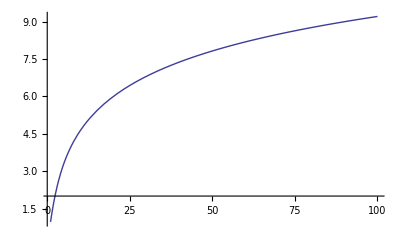

```mathematica
Plot[%,{a,1,100}]
```

```mathematica
EE=((xi-mu)^2+dt^2)^(1/2);cond={mu->-10,dt->1};cond2={mu->100,dt->0.01}
```

{mu→100,dt→0.01}

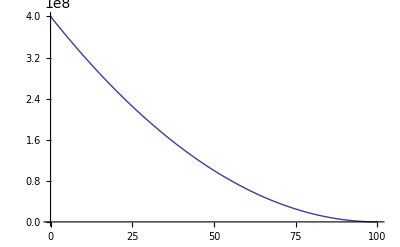

```mathematica
Plot[((EE-(xi-mu))/(EE+(xi-mu)))/.cond2,{xi,0,100},PlotRange->Full]
```

```mathematica
Integrate[k k /(k k + k1 k1),{k,0,k2}]
```

If[Im[k1/k2]≥1||1+Im[k1/k2]≤0||k1/k2∈Reals||Re[k1/k2]≠0,k2-k1 ArcTan[k2/k1],Integrate[(k2^3 k^2)/(k1^2+k2^2 k^2),{k,0,1},Assumptions→!(Im[k1/k2]≥1||1+Im[k1/k2]≤0||k1/k2∈Reals||Re[k1/k2]≠0)]]